```mathematica
M11 = -Ω^2(1+γ ϵ^2/2);
M12 = 0;
M13 =(-I Subscript[K, X] (n+1) (1+γ ϵ^2/2))/γ;
M21 = ϵ^2 Subscript[K, X] Subscript[K, Y] Z;
M22 = -Ω^2(1+γ ϵ^2/2)+ϵ^2 Subscript[K, X]^2 Z;
M23 = (-I Subscript[K, Y] (n+1) (1+γ ϵ^2/2))/γ;
M31 = (I Subscript[K, X])/γ(1+ (3γ ϵ^2)/2+(ϵ^2 Subscript[K, X]^2 Z(1+γ ϵ^2/2))/(Ω^2(1+γ ϵ^2/2)));
M32 = (I Subscript[K, Y])/γ(1+ (γ ϵ^2)/2+(ϵ^2 Subscript[K, X]^2 Z(1+γ ϵ^2/2))/(Ω^2(1+γ ϵ^2/2)));
M33 = (-Ω^2(1+γ ϵ^2/2)+ϵ^2 Subscript[K, X]^2 Z)/(n+1);
Subscript[h, X] = I Subscript[K, X] Z χ;
Subscript[h, Y] = I Subscript[K, Y] Z χ (1+ ϵ^2);
h0 = (1+ϵ^2(1+(Subscript[K, X]^2 Z (γ-(n+1)(1+γ ϵ^2/2 )))/((n+1)γ Ω^2(1+γ ϵ^2/2))));
h1 = Z/(n+1)(1+ϵ^2(1+(Subscript[K, X]^2 Z)/(Ω^2(1+γ ϵ^2/2))));
Subscript[h, Z] = χ*h0+D[χ[Z],Z]*h1
Minv = Inverse[({{M11,M12,M13},{M21,M22,M23},{M31,M32,M33}})];
```

χ (1+ϵ^2 (1+(Z (γ-(1+n) (1+(γ ϵ^2)/2)) K_X^2)/((1+n) γ (1+(γ ϵ^2)/2) Ω^2)))+(Z (1+ϵ^2 (1+(Z K_X^2)/((1+(γ ϵ^2)/2) Ω^2))) χ'[Z])/(1+n)

```mathematica
ufullhaschi = Dot[Minv, {Subscript[h, X]/χ, Subscript[h, Y]/χ, h0}];
uxchi = ufullhaschi[[1]];
uychi = ufullhaschi[[2]];
uzchi = ufullhaschi[[3]];

ufullhasderivativeofchi = Dot[Minv, {0, 0, h1}];
uxdervchi = ufullhasderivativeofchi [[1]];
uydervchi = ufullhasderivativeofchi [[2]];
uzdervchi = ufullhasderivativeofchi [[3]];

ux = uxchi *χ+ uxdervchi*D[χ[Z],Z];
uy = uychi *χ+ uydervchi*D[χ[Z],Z];
uz = uzchi *χ+ uzdervchi*D[χ[Z],Z];
```

```mathematica
(*----------------------------------------------------------------------------*)
(*i kx ux + i ky uy + dz(uz) = χ;
i kx ux + i ky uy + dz(uz) - χ = 0;
SchrodingerformSECONDDERIVATIVEchi D^2 χ + SchrodingerformFIRSTDERIVATIVEchi Dχ + SchrodingerformZERODERIVATIVEchi_original χ - χ= 0;
SchrodingerformSECONDDERIVATIVEchi D^2 χ + SchrodingerformFIRSTDERIVATIVEchi Dχ + (SchrodingerformZERODERIVATIVEchi_original - 1) χ = 0;
SchrodingerformSECONDDERIVATIVEchi D^2 χ + SchrodingerformFIRSTDERIVATIVEchi Dχ + (SchrodingerformZERODERIVATIVEchi) χ = 0*)

SchrodingerformZERODERIVATIVEchi = I *Subscript[K, X] *uxchi +I *Subscript[K, Y] *uychi +D[uzchi ,Z] -1;
SchrodingerformFIRSTDERIVATIVEchi = I *Subscript[K, X] *uxdervchi +I *Subscript[K, Y] *uydervchi +(uzchi +D[uzdervchi,Z]);
SchrodingerformSECONDDERIVATIVEchi = 0+0+uzdervchi
```

(Z (Ω^4+γ ϵ^2 Ω^4+1/4 γ^2 ϵ^4 Ω^4-Z ϵ^2 Ω^2 K_X^2-1/2 Z γ ϵ^4 Ω^2 K_X^2) (1+ϵ^2 (1+(Z K_X^2)/((1+(γ ϵ^2)/2) Ω^2))))/((1+n) ((-((1+(γ ϵ^2)/2) Ω^2)+Z ϵ^2 K_X^2) (-((1+(γ ϵ^2)/2) Ω^2 (-((1+(γ ϵ^2)/2) Ω^2)+Z ϵ^2 K_X^2))/(1+n)-((1+n) (1+(γ ϵ^2)/2) K_X^2 (1+(3 γ ϵ^2)/2+(Z ϵ^2 K_X^2)/Ω^2))/γ^2)-(ⅈ (1+(γ ϵ^2)/2+(Z ϵ^2 K_X^2)/Ω^2) K_Y ((ⅈ (1+n) (1+(γ ϵ^2)/2)^2 Ω^2 K_Y)/γ+(ⅈ (1+n) Z ϵ^2 (1+(γ ϵ^2)/2) K_X^2 K_Y)/γ))/γ))

```mathematica
(*----------------------------------------------------------------------------*)
(* D^2 χ + f(Z) * Dχ + r(Z)* χ = 0, Following the arxiv paper v2, https://arxiv.org/pdf/1812.06947v2.pdf *)

f[Z_]:=SchrodingerformFIRSTDERIVATIVEchi/SchrodingerformSECONDDERIVATIVEchi;
r[Z_]:=SchrodingerformZERODERIVATIVEchi/SchrodingerformSECONDDERIVATIVEchi;
```

```mathematica
(*-------------------------------------------------------------------------------------*)
(*Tolstoy equation/Normal-form here*)
(*(d^2 ψ)/dZ^2 + Q(Z,ϵ) ψ = 0*)
(*(d^2 ψ)/dZ^2 + Γ^2(Z,ϵ) ψ = 0*)

Q[Z_]:=r[Z]-(f[Z])^2/4-D[f[Z],Z]/2;
Gammafreq [Z_]:= √Q[Z];
Gammaexpanded = Normal[Series[Gammafreq[Z],{ϵ,0,2}]]
```

1/2 √((-2 n γ^2 Ω^2-n^2 γ^2 Ω^2+4 Z γ^2 Ω^4-4 Z K_X^2-8 n Z K_X^2-4 n^2 Z K_X^2+4 n Z γ K_X^2+4 n^2 Z γ K_X^2-4 Z^2 γ^2 Ω^2 K_X^2-4 Z K_Y^2-8 n Z K_Y^2-4 n^2 Z K_Y^2+4 n Z γ K_Y^2+4 n^2 Z γ K_Y^2-4 Z^2 γ^2 Ω^2 K_Y^2)/(Z^2 γ^2 Ω^2))+(Z ϵ^2 √((-2 n γ^2 Ω^2-n^2 γ^2 Ω^2+4 Z γ^2 Ω^4-4 Z K_X^2-8 n Z K_X^2-4 n^2 Z K_X^2+4 n Z γ K_X^2+4 n^2 Z γ K_X^2-4 Z^2 γ^2 Ω^2 K_X^2-4 Z K_Y^2-8 n Z K_Y^2-4 n^2 Z K_Y^2+4 n Z γ K_Y^2+4 n^2 Z γ K_Y^2-4 Z^2 γ^2 Ω^2 K_Y^2)/(Z^2 γ^2 Ω^2)) (-2 γ^4 Ω^10+γ^5 Ω^10+4 γ^2 Ω^6 K_X^2+8 n γ^2 Ω^6 K_X^2+4 n^2 γ^2 Ω^6 K_X^2-4 γ^3 Ω^6 K_X^2-8 n γ^3 Ω^6 K_X^2-4 n^2 γ^3 Ω^6 K_X^2+3 n γ^4 Ω^6 K_X^2+2 n^2 γ^4 Ω^6 K_X^2-2 Z γ^4 Ω^8 K_X^2-2 Ω^2 K_X^4-8 n Ω^2 K_X^4-12 n^2 Ω^2 K_X^4-8 n^3 Ω^2 K_X^4-2 n^4 Ω^2 K_X^4+3 γ Ω^2 K_X^4+12 n γ Ω^2 K_X^4+18 n^2 γ Ω^2 K_X^4+12 n^3 γ Ω^2 K_X^4+3 n^4 γ Ω^2 K_X^4-n γ^2 Ω^2 K_X^4-4 n^2 γ^2 Ω^2 K_X^4-5 n^3 γ^2 Ω^2 K_X^4-2 n^4 γ^2 Ω^2 K_X^4-4 Z γ^3 Ω^4 K_X^4-6 n Z γ^3 Ω^4 K_X^4-2 n^2 Z γ^3 Ω^4 K_X^4+4 Z^2 γ^4 Ω^6 K_X^4+2 Z K_X^6+8 n Z K_X^6+12 n^2 Z K_X^6+8 n^3 Z K_X^6+2 n^4 Z K_X^6+2 n Z γ K_X^6+6 n^2 Z γ K_X^6+6 n^3 Z γ K_X^6+2 n^4 Z γ K_X^6-4 Z^2 γ^2 Ω^2 K_X^6-8 n Z^2 γ^2 Ω^2 K_X^6-4 n^2 Z^2 γ^2 Ω^2 K_X^6+4 γ^2 Ω^6 K_Y^2+8 n γ^2 Ω^6 K_Y^2+4 n^2 γ^2 Ω^6 K_Y^2-2 γ^3 Ω^6 K_Y^2-4 n γ^3 Ω^6 K_Y^2-2 n^2 γ^3 Ω^6 K_Y^2-4 Ω^2 K_X^2 K_Y^2-16 n Ω^2 K_X^2 K_Y^2-24 n^2 Ω^2 K_X^2 K_Y^2-16 n^3 Ω^2 K_X^2 K_Y^2-4 n^4 Ω^2 K_X^2 K_Y^2+4 γ Ω^2 K_X^2 K_Y^2+16 n γ Ω^2 K_X^2 K_Y^2+24 n^2 γ Ω^2 K_X^2 K_Y^2+16 n^3 γ Ω^2 K_X^2 K_Y^2+4 n^4 γ Ω^2 K_X^2 K_Y^2+n γ^2 Ω^2 K_X^2 K_Y^2-3 n^3 γ^2 Ω^2 K_X^2 K_Y^2-2 n^4 γ^2 Ω^2 K_X^2 K_Y^2-4 Z γ^2 Ω^4 K_X^2 K_Y^2-8 n Z γ^2 Ω^4 K_X^2 K_Y^2-4 n^2 Z γ^2 Ω^4 K_X^2 K_Y^2-8 Z γ^3 Ω^4 K_X^2 K_Y^2-6 n Z γ^3 Ω^4 K_X^2 K_Y^2+2 n^2 Z γ^3 Ω^4 K_X^2 K_Y^2+8 Z K_X^4 K_Y^2+32 n Z K_X^4 K_Y^2+48 n^2 Z K_X^4 K_Y^2+32 n^3 Z K_X^4 K_Y^2+8 n^4 Z K_X^4 K_Y^2-4 Z^2 γ^2 Ω^2 K_X^4 K_Y^2-8 n Z^2 γ^2 Ω^2 K_X^4 K_Y^2-4 n^2 Z^2 γ^2 Ω^2 K_X^4 K_Y^2-2 Ω^2 K_Y^4-8 n Ω^2 K_Y^4-12 n^2 Ω^2 K_Y^4-8 n^3 Ω^2 K_Y^4-2 n^4 Ω^2 K_Y^4+γ Ω^2 K_Y^4+4 n γ Ω^2 K_Y^4+6 n^2 γ Ω^2 K_Y^4+4 n^3 γ Ω^2 K_Y^4+n^4 γ Ω^2 K_Y^4+6 Z K_X^2 K_Y^4+24 n Z K_X^2 K_Y^4+36 n^2 Z K_X^2 K_Y^4+24 n^3 Z K_X^2 K_Y^4+6 n^4 Z K_X^2 K_Y^4-2 n Z γ K_X^2 K_Y^4-6 n^2 Z γ K_X^2 K_Y^4-6 n^3 Z γ K_X^2 K_Y^4-2 n^4 Z γ K_X^2 K_Y^4))/(2 Ω^2 (γ^2 Ω^4-K_X^2-2 n K_X^2-n^2 K_X^2-K_Y^2-2 n K_Y^2-n^2 K_Y^2) (-2 n γ^2 Ω^2-n^2 γ^2 Ω^2+4 Z γ^2 Ω^4-4 Z K_X^2-8 n Z K_X^2-4 n^2 Z K_X^2+4 n Z γ K_X^2+4 n^2 Z γ K_X^2-4 Z^2 γ^2 Ω^2 K_X^2-4 Z K_Y^2-8 n Z K_Y^2-4 n^2 Z K_Y^2+4 n Z γ K_Y^2+4 n^2 Z γ K_Y^2-4 Z^2 γ^2 Ω^2 K_Y^2))

```mathematica
numeratorofintendedterm = (-2 γ^4 Ω^10+γ^5 Ω^10+4 γ^2 Ω^6 Subscript[K, X]^2+8 n γ^2 Ω^6 Subscript[K, X]^2+4 n^2 γ^2 Ω^6 Subscript[K, X]^2-4 γ^3 Ω^6 Subscript[K, X]^2-8 n γ^3 Ω^6 Subscript[K, X]^2-4 n^2 γ^3 Ω^6 Subscript[K, X]^2+3 n γ^4 Ω^6 Subscript[K, X]^2+2 n^2 γ^4 Ω^6 Subscript[K, X]^2-2 Z γ^4 Ω^8 Subscript[K, X]^2-2 Ω^2 Subscript[K, X]^4-8 n Ω^2 Subscript[K, X]^4-12 n^2 Ω^2 Subscript[K, X]^4-8 n^3 Ω^2 Subscript[K, X]^4-2 n^4 Ω^2 Subscript[K, X]^4+3 γ Ω^2 Subscript[K, X]^4+12 n γ Ω^2 Subscript[K, X]^4+18 n^2 γ Ω^2 Subscript[K, X]^4+12 n^3 γ Ω^2 Subscript[K, X]^4+3 n^4 γ Ω^2 Subscript[K, X]^4-n γ^2 Ω^2 Subscript[K, X]^4-4 n^2 γ^2 Ω^2 Subscript[K, X]^4-5 n^3 γ^2 Ω^2 Subscript[K, X]^4-2 n^4 γ^2 Ω^2 Subscript[K, X]^4-4 Z γ^3 Ω^4 Subscript[K, X]^4-6 n Z γ^3 Ω^4 Subscript[K, X]^4-2 n^2 Z γ^3 Ω^4 Subscript[K, X]^4+4 Z^2 γ^4 Ω^6 Subscript[K, X]^4+2 Z Subscript[K, X]^6+8 n Z Subscript[K, X]^6+12 n^2 Z Subscript[K, X]^6+8 n^3 Z Subscript[K, X]^6+2 n^4 Z Subscript[K, X]^6+2 n Z γ Subscript[K, X]^6+6 n^2 Z γ Subscript[K, X]^6+6 n^3 Z γ Subscript[K, X]^6+2 n^4 Z γ Subscript[K, X]^6-4 Z^2 γ^2 Ω^2 Subscript[K, X]^6-8 n Z^2 γ^2 Ω^2 Subscript[K, X]^6-4 n^2 Z^2 γ^2 Ω^2 Subscript[K, X]^6+4 γ^2 Ω^6 Subscript[K, Y]^2+8 n γ^2 Ω^6 Subscript[K, Y]^2+4 n^2 γ^2 Ω^6 Subscript[K, Y]^2-2 γ^3 Ω^6 Subscript[K, Y]^2-4 n γ^3 Ω^6 Subscript[K, Y]^2-2 n^2 γ^3 Ω^6 Subscript[K, Y]^2-4 Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2-16 n Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2-24 n^2 Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2-16 n^3 Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2-4 n^4 Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2+4 γ Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2+16 n γ Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2+24 n^2 γ Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2+16 n^3 γ Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2+4 n^4 γ Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2+n γ^2 Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2-3 n^3 γ^2 Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2-2 n^4 γ^2 Ω^2 Subscript[K, X]^2 Subscript[K, Y]^2-4 Z γ^2 Ω^4 Subscript[K, X]^2 Subscript[K, Y]^2-8 n Z γ^2 Ω^4 Subscript[K, X]^2 Subscript[K, Y]^2-4 n^2 Z γ^2 Ω^4 Subscript[K, X]^2 Subscript[K, Y]^2-8 Z γ^3 Ω^4 Subscript[K, X]^2 Subscript[K, Y]^2-6 n Z γ^3 Ω^4 Subscript[K, X]^2 Subscript[K, Y]^2+2 n^2 Z γ^3 Ω^4 Subscript[K, X]^2 Subscript[K, Y]^2+8 Z Subscript[K, X]^4 Subscript[K, Y]^2+32 n Z Subscript[K, X]^4 Subscript[K, Y]^2+48 n^2 Z Subscript[K, X]^4 Subscript[K, Y]^2+32 n^3 Z Subscript[K, X]^4 Subscript[K, Y]^2+8 n^4 Z Subscript[K, X]^4 Subscript[K, Y]^2-4 Z^2 γ^2 Ω^2 Subscript[K, X]^4 Subscript[K, Y]^2-8 n Z^2 γ^2 Ω^2 Subscript[K, X]^4 Subscript[K, Y]^2-4 n^2 Z^2 γ^2 Ω^2 Subscript[K, X]^4 Subscript[K, Y]^2-2 Ω^2 Subscript[K, Y]^4-8 n Ω^2 Subscript[K, Y]^4-12 n^2 Ω^2 Subscript[K, Y]^4-8 n^3 Ω^2 Subscript[K, Y]^4-2 n^4 Ω^2 Subscript[K, Y]^4+γ Ω^2 Subscript[K, Y]^4+4 n γ Ω^2 Subscript[K, Y]^4+6 n^2 γ Ω^2 Subscript[K, Y]^4+4 n^3 γ Ω^2 Subscript[K, Y]^4+n^4 γ Ω^2 Subscript[K, Y]^4+6 Z Subscript[K, X]^2 Subscript[K, Y]^4+24 n Z Subscript[K, X]^2 Subscript[K, Y]^4+36 n^2 Z Subscript[K, X]^2 Subscript[K, Y]^4+24 n^3 Z Subscript[K, X]^2 Subscript[K, Y]^4+6 n^4 Z Subscript[K, X]^2 Subscript[K, Y]^4-2 n Z γ Subscript[K, X]^2 Subscript[K, Y]^4-6 n^2 Z γ Subscript[K, X]^2 Subscript[K, Y]^4-6 n^3 Z γ Subscript[K, X]^2 Subscript[K, Y]^4-2 n^4 Z γ Subscript[K, X]^2 Subscript[K, Y]^4);
```

```mathematica
FullSimplify[Coefficient[numeratorofintendedterm  ,Z,2]]
```

-4 γ^2 Ω^2 K_X^4 (-γ^2 Ω^4+(1+n)^2 K_X^2+(1+n)^2 K_Y^2)

```mathematica
FullSimplify[Coefficient[numeratorofintendedterm /(2 Ω^2 *(γ^2 Ω^4-Subscript[K, X]^2-2 n Subscript[K, X]^2-n^2 Subscript[K, X]^2-Subscript[K, Y]^2-2 n Subscript[K, Y]^2-n^2 Subscript[K, Y]^2)*(γ Ω *2I γ Ω K)) ,Z,2]]
```

-(ⅈ K_X^4)/(K Ω^2)

```mathematica
FullSimplify[Coefficient[numeratorofintendedterm /(2 Ω^2 *(γ^2 Ω^4-Subscript[K, X]^2-2 n Subscript[K, X]^2-n^2 Subscript[K, X]^2-Subscript[K, Y]^2-2 n Subscript[K, Y]^2-n^2 Subscript[K, Y]^2)*(γ Ω *2I γ Ω K)) ,Z,2]/.Subscript[K, X]->K Cos[θ]/.Subscript[K, Y]->K Sin[θ]] (*This is Subscript[a, 2] in Subscript[Γ, 2]=(Subscript[a, 2] Z^2+Subscript[a, 1] Z +Subscript[a, 0])/(√((Z-α)(Z-β)))*)
```

-(ⅈ K^3 Cos[θ]^4)/Ω^2

```mathematica
FullSimplify[Coefficient[numeratorofintendedterm /(2 Ω^2 *(γ^2 Ω^4-Subscript[K, X]^2-2 n Subscript[K, X]^2-n^2 Subscript[K, X]^2-Subscript[K, Y]^2-2 n Subscript[K, Y]^2-n^2 Subscript[K, Y]^2)*(γ Ω *2I γ Ω K)) ,Z,1]/.Subscript[K, X]->K Cos[θ]/.Subscript[K, Y]->K Sin[θ]] (*This is Subscript[a, 1] in Subscript[Γ, 2]=(Subscript[a, 2] Z^2+Subscript[a, 1] Z +Subscript[a, 0])/(√((Z-α)(Z-β)))*)
```

(ⅈ K Cos[θ]^2 (2 K^4 (1+n)^4-K^2 (1+n) γ^2 (1+n+3 γ) Ω^4-γ^4 Ω^8+K^2 (1+n) (K^2 (1+n)^2 (-1+n (-1+γ))+γ^2 (1+n+γ-n γ) Ω^4) Cos[2 θ]))/(2 γ^2 Ω^4 (K^2 (1+n)^2-γ^2 Ω^4))

```mathematica
FullSimplify[Coefficient[numeratorofintendedterm /(2 Ω^2 *(γ^2 Ω^4-Subscript[K, X]^2-2 n Subscript[K, X]^2-n^2 Subscript[K, X]^2-Subscript[K, Y]^2-2 n Subscript[K, Y]^2-n^2 Subscript[K, Y]^2)*(γ Ω *2I γ Ω K)) ,Z,0]/.Subscript[K, X]->K Cos[θ]/.Subscript[K, Y]->K Sin[θ]] (*This is Subscript[a, 0] in Subscript[Γ, 2]=(Subscript[a, 2] Z^2+Subscript[a, 1] Z +Subscript[a, 0])/(√((Z-α)(Z-β)))*)
```

-1/(16 K^3 (1+n)^2 γ^2 Ω^2-16 K γ^4 Ω^6)ⅈ (K^4 (1+n)^2 (8 (1+n)^2-8 (1+n)^2 γ+n (1+4 n) γ^2)-2 K^2 γ^2 (8 (1+n)^2-6 (1+n)^2 γ+n (3+2 n) γ^2) Ω^4-4 (-2+γ) γ^4 Ω^8+2 K^2 γ (K^2 (1+n)^2 (-2+n (-4+2 n (-1+γ)+γ))+γ^2 (2 (1+n)^2-n (3+2 n) γ) Ω^4) Cos[2 θ]+K^4 n (1+n)^2 γ^2 Cos[4 θ])

```mathematica
lamb2TPpolynomial = Simplify[((-2 n γ^2 Ω^2-n^2 γ^2 Ω^2+4 Z γ^2 Ω^4-4 Z Subscript[K, X]^2-8 n Z Subscript[K, X]^2-4 n^2 Z Subscript[K, X]^2+4 n Z γ Subscript[K, X]^2+4 n^2 Z γ Subscript[K, X]^2-4 Z^2 γ^2 Ω^2 Subscript[K, X]^2-4 Z Subscript[K, Y]^2-8 n Z Subscript[K, Y]^2-4 n^2 Z Subscript[K, Y]^2+4 n Z γ Subscript[K, Y]^2+4 n^2 Z γ Subscript[K, Y]^2-4 Z^2 γ^2 Ω^2 Subscript[K, Y]^2)/(-4 γ^2 Ω^2 K^2))/.Subscript[K, X]->K Cos[θ]/.Subscript[K, Y]->K Sin[θ]] (*This has the form (Z-α)(Z-β) = Z^2 - (α+β)Z + α β = 0. *)
```

(2 n+n^2-4 Z Ω^2)/(4 K^2)+(Z (1-n (-2+γ)-n^2 (-1+γ)+Z γ^2 Ω^2))/(γ^2 Ω^2)

```mathematica
FullSimplify[Coefficient[lamb2TPpolynomial ,Z,2]] (*This is 1.*)
```

1

```mathematica
FullSimplify[Coefficient[lamb2TPpolynomial ,Z,1]]  (*This is -(α+β). *)
```

((1+n) (1+n-n γ))/(γ^2 Ω^2)-Ω^2/K^2

```mathematica
FullSimplify[Coefficient[lamb2TPpolynomial ,Z,0]]  (*This is α β. *)
```

(n (2+n))/(4 K^2)

```mathematica
Integrate[Subscript[a, 0]/(√((Z-α)(Z-β))),{Z,α,β}]
```

2 √(1/(α-β)) √(α-β) ArcSinh[(√(-α+β))/(√(α-β))] a_0

```mathematica
2  ArcSinh[1/(√(-1))] Subscript[a, 0]
```

-ⅈ π a_0

```mathematica
Integrate[(Subscript[a, 1] Z)/(√((Z-α)(Z-β))),{Z,α,β}]
```

(√(1/(α-β)) √(-(α-β)^2) (α+β) ArcSinh[(√(-α+β))/(√(α-β))] a_1)/(√(-α+β))

```mathematica
(α+β) ArcSinh[1/(√(-1))] Subscript[a, 1]
```

-1/2 ⅈ π (α+β) a_1

```mathematica
Integrate[(Subscript[a, 2] Z^2)/(√((Z-α)(Z-β))),{Z,α,β}]
```

(√(1/(α-β)) √(-(α-β)^2) (3 α^2+2 α β+3 β^2) ArcSinh[(√(-α+β))/(√(α-β))] a_2)/(4 √(-α+β))

```mathematica
((3 α^2+2 α β+3 β^2) ArcSinh[1/(√(-1))] Subscript[a, 2])/4
```

-1/8 ⅈ π (3 α^2+2 α β+3 β^2) a_2

```mathematica
Integrate[(A √((Z-α)(Z-β)))/Z,Z]
```

(A √(Z-α) (-√(α-β) (-Z+β) (α+β) ArcSinh[(√(Z-α))/(√(α-β))]+√((Z-β)/(α-β)) (-α+β) (√(Z-α) (Z-β)+2 √α √(Z-β) √β ArcTanh[(√(Z-α) √β)/(√α √(Z-β))])))/(√((Z-α) (Z-β)) √((Z-β)/(α-β)) (-α+β))

```mathematica
Series[Expand[Integrate[(A √((Z-α)(Z-β)))/Z,Z]]/.Z->(α+ϵ^2 c),{ϵ,0,3}]
```

(2 A c √(c (α-β) ϵ^2) ϵ^3)/(3 α ϵ)+O[ϵ]^4

```mathematica
FullSimplify[2+(Cos[θ])^2-12(Cos[θ])^4]
```

2+Cos[θ]^2-12 Cos[θ]^4

```mathematica
TrigReduce[2+Cos[θ]^2-12 Cos[θ]^4]
```

1/2 (-4-11 Cos[2 θ]-3 Cos[4 θ])

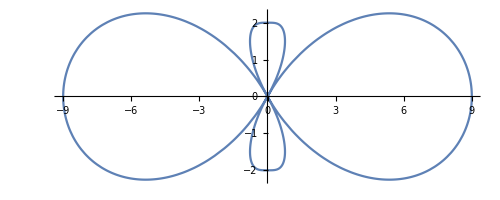

```mathematica
PolarPlot[1/2 (-4-11 Cos[2 θ]-3 Cos[4 θ]),{θ,0,2 π}]
```

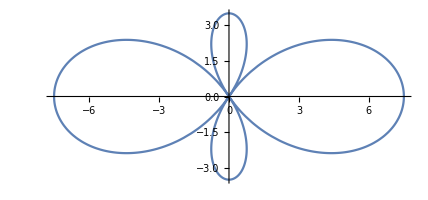

```mathematica
PolarPlot[1/2 (-4-11 Cos[2 θ]),{θ,0,2 π}]
```

```mathematica
Series[Tan[c+d],{d,0,2}]
```

Tan[c]+(1+Tan[c]^2) d+(Tan[c]+Tan[c]^3) d^2+O[d]^3

```mathematica
Series[Log[1+d],{d,0,2}]
```

d-d^2/2+O[d]^3